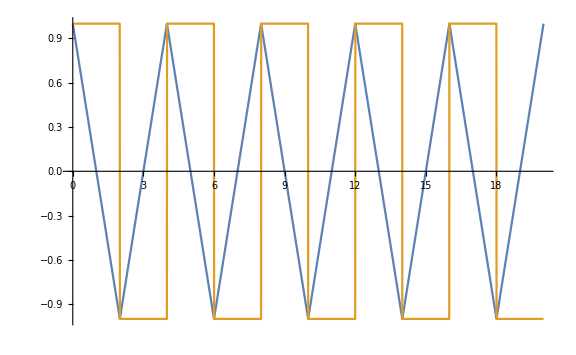

```mathematica
(* Single c-bit dynamics under constant I_i and T. Note taht in the code, I_i is z and m_i is s *)

z=0; (* the input to the c-bit, z, can be any value between -∞,+∞* try small values not to break in the beginning*)  
T=1;
tsim=20;
sol=First@NDSolve[{x'[t]==-s[t]+Tanh[z/T],x[0]==1,s[0]==1,WhenEvent[{{x[t]==-1,x[t]==1}},s[t]->(Sign[Round[x[t]]])]},{x,s},{t,0,tsim},DiscreteVariables->s];
xt= x/.sol;st = s/.sol;
Plot[{x[t]/.sol,s[t]/.sol},{t,0,tsim},ImageSize-> Large]

timeValues = Range[0,tsim,0.01];
xtValues=Evaluate[x[t]/. sol]/. t->timeValues;
stValues=Evaluate[s[t]/. sol]/. t->timeValues;
```

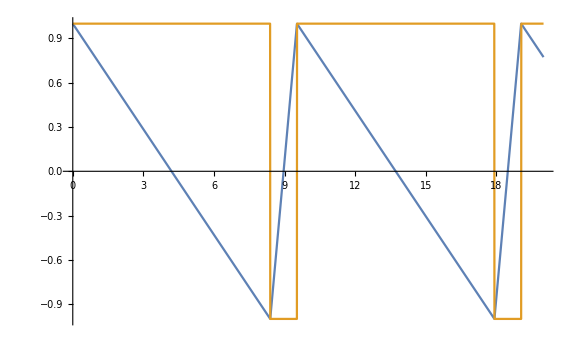

```mathematica
z=1; (* z can be any value between -∞,+∞* try small values not to break in the beginning*)  
T=1;
tsim=20;
sol=First@NDSolve[{x'[t]==-s[t]+Tanh[z/T],x[0]==1,s[0]==1,WhenEvent[{{x[t]==-1,x[t]==1}},s[t]->(Sign[Round[x[t]]])]},{x,s},{t,0,tsim},DiscreteVariables->s];
xt= x/.sol;st = s/.sol;
Plot[{x[t]/.sol,s[t]/.sol},{t,0,tsim},ImageSize-> Large]

timeValues = Range[0,tsim,0.01];
xtValues=Evaluate[x[t]/. sol]/. t->timeValues;
stValues=Evaluate[s[t]/. sol]/. t->timeValues;
```